# QVSP Dispersion Relation

Along the lines of Arnau’s Journal preprint

```mathematica
ClearAll["Global`*"]
```

## Definitions

#### Rotation Matrices and Q’s

Eqs.(32-34) in conjunction with (18)

```mathematica
Rx = 1/(√2)*({{√2, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, -1}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, √2, 0, 0}, {0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, -1, 0}});
```

```mathematica
Ry = 1/(√2)*({{0, √2, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, -1}, {0, 0, -1, 1, 0, 0}, {0, 0, 0, 0, √2, 0}, {-1, 0, 0, 0, 0, 1}, {0, 0, -1, -1, 0, 0}});
```

```mathematica
Rz = 1/(√2)*({{0, 0, √2, 0, 0, 0}, {1, 0, 0, 0, -1, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 0, 0, 0, √2}, {1, 0, 0, 0, 1, 0}, {0, 1, 0, -1, 0, 0}});
```

```mathematica
adagQx = Transpose[Rx].DiagonalMatrix[{0,1,1,0,-1,-1}].Rx
```

{{0,0,0,0,0,0},{0,0,0,0,0,-1},{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,1,0,0,0},{0,-1,0,0,0,0}}

```mathematica
MatrixForm[adagQx]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0)

```mathematica
adagQy = Transpose[Ry].DiagonalMatrix[{0,1,1,0,-1,-1}].Ry
```

{{0,0,0,0,0,1},{0,0,0,0,0,0},{0,0,0,-1,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0}}

```mathematica
MatrixForm[adagQy]
```

(0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
adagQz = Transpose[Rz].DiagonalMatrix[{0,1,1,0,-1,-1}].Rz
```

{{0,0,0,0,-1,0},{0,0,0,1,0,0},{0,0,0,0,0,0},{0,1,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
MatrixForm[adagQz]
```

(0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### Stencils

Eqs.(23,24), but for nonlinear case modified to (35)!

```mathematica
Δ= 1/4; (* resolution, change here *)
```

```mathematica
Sm3 =1/Δ *DiagonalMatrix[{-1/12,-1/12,-1/12,0,0,0}];
```

```mathematica
Sm2 =1/Δ * DiagonalMatrix[{1/2,1/2,1/2,0,0,0}];
```

```mathematica
Sm1 =1/Δ * DiagonalMatrix[{-3/2,-3/2,-3/2,-1/4,-1/4,-1/4}];
```

```mathematica
S0 =1/Δ * DiagonalMatrix[{5/6,5/6,5/6,(- 5)/6,(- 5)/6,-5/6}];
```

```mathematica
Sp1 = 1/Δ *DiagonalMatrix[{1/4,1/4,1/4,3/2,3/2,3/2}];
```

```mathematica
Sp2 =1/Δ * DiagonalMatrix[{0,0,0,-1/2,-1/2,-1/2}];
```

```mathematica
Sp3 =1/Δ * DiagonalMatrix[{0,0,0,1/12,1/12,1/12}];
```

#### Summations

```mathematica
Transpose[Rx].Sm3.Rx - Sm3
```

{{0,0,0,0,0,0},{0,1/6,0,0,0,1/6},{0,0,1/6,0,-1/6,0},{0,0,0,0,0,0},{0,0,-1/6,0,-1/6,0},{0,1/6,0,0,0,-1/6}}

```mathematica
(*kx*=0;ky=0;*)
```

```mathematica
xm3 = adagQx.Transpose[Rx].Sp3.Rx*ⅇ^(-ⅈ*(3)*kx*Δ)
```

{{0,0,0,0,0,0},{0,-1/6 ⅇ^(-(3 ⅈ kx)/4),0,0,0,-1/6 ⅇ^(-(3 ⅈ kx)/4)},{0,0,-1/6 ⅇ^(-(3 ⅈ kx)/4),0,1/6 ⅇ^(-(3 ⅈ kx)/4),0},{0,0,0,0,0,0},{0,0,1/6 ⅇ^(-(3 ⅈ kx)/4),0,-1/6 ⅇ^(-(3 ⅈ kx)/4),0},{0,-1/6 ⅇ^(-(3 ⅈ kx)/4),0,0,0,-1/6 ⅇ^(-(3 ⅈ kx)/4)}}

```mathematica
MatrixForm[xm3.{0,0,1,0,-1,0}]
```

(0
0
-1/3 ⅇ^(-(3 ⅈ kx)/4)
0
1/3 ⅇ^(-(3 ⅈ kx)/4)
0)

```mathematica
ym3 = adagQy.Transpose[Ry].Sm3.Ry*ⅇ^(-ⅈ*(-3)*ky*Δ)
```

{{-1/6 ⅇ^((3 ⅈ ky)/4),0,0,0,0,-1/6 ⅇ^((3 ⅈ ky)/4)},{0,0,0,0,0,0},{0,0,-1/6 ⅇ^((3 ⅈ ky)/4),1/6 ⅇ^((3 ⅈ ky)/4),0,0},{0,0,1/6 ⅇ^((3 ⅈ ky)/4),-1/6 ⅇ^((3 ⅈ ky)/4),0,0},{0,0,0,0,0,0},{-1/6 ⅇ^((3 ⅈ ky)/4),0,0,0,0,-1/6 ⅇ^((3 ⅈ ky)/4)}}

```mathematica
MatrixForm[ym3]
```

(-1/6 ⅇ^((3 ⅈ ky)/4) | 0 | 0 | 0 | 0 | -1/6 ⅇ^((3 ⅈ ky)/4)
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/6 ⅇ^((3 ⅈ ky)/4) | 1/6 ⅇ^((3 ⅈ ky)/4) | 0 | 0
0 | 0 | 1/6 ⅇ^((3 ⅈ ky)/4) | -1/6 ⅇ^((3 ⅈ ky)/4) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
-1/6 ⅇ^((3 ⅈ ky)/4) | 0 | 0 | 0 | 0 | -1/6 ⅇ^((3 ⅈ ky)/4))

```mathematica
zm3[kz_]= adagQz.Transpose[Rz].Sm3.Rz*ⅇ^(-ⅈ*(-3)*kz*Δ)
```

{{-1/6 ⅇ^((3 ⅈ kz)/4),0,0,0,1/6 ⅇ^((3 ⅈ kz)/4),0},{0,-1/6 ⅇ^((3 ⅈ kz)/4),0,-1/6 ⅇ^((3 ⅈ kz)/4),0,0},{0,0,0,0,0,0},{0,-1/6 ⅇ^((3 ⅈ kz)/4),0,-1/6 ⅇ^((3 ⅈ kz)/4),0,0},{1/6 ⅇ^((3 ⅈ kz)/4),0,0,0,-1/6 ⅇ^((3 ⅈ kz)/4),0},{0,0,0,0,0,0}}

```mathematica
xm2 = adagQx.Transpose[Rx].Sm2.Rx*ⅇ^(-ⅈ*(-2)*kx*Δ) ;
```

```mathematica
ym2 = adagQy.Transpose[Ry].Sm2.Ry*ⅇ^(-ⅈ*(-2)*ky*Δ) ;
```

```mathematica
zm2[kz_] = adagQz.Transpose[Rz].Sm2.Rz*ⅇ^(-ⅈ*(-2)*kz*Δ) ;
```

```mathematica
xm1 = adagQx.Transpose[Rx].Sm1.Rx*ⅇ^(-ⅈ*(-1)*kx*Δ) ;
```

```mathematica
ym1 = adagQy.Transpose[Ry].Sm1.Ry*ⅇ^(-ⅈ*(-1)*ky*Δ) ;
```

```mathematica
zm1[kz_] = adagQz.Transpose[Rz].Sm1.Rz*ⅇ^(-ⅈ*(-1)*kz*Δ) ;
```

```mathematica
x0 = adagQx.Transpose[Rx].S0.Rx ;
```

```mathematica
y0 = adagQy.Transpose[Ry].S0.Ry ;
```

```mathematica
z0 = adagQz.Transpose[Rz].S0 .Rz;
```

```mathematica
xp1 = adagQx.Transpose[Rx].Sp1.Rx*ⅇ^(-ⅈ*(1)*kx*Δ) ;
```

```mathematica
yp1 = adagQy.Transpose[Ry].Sp1.Ry*ⅇ^(-ⅈ*(1)*ky*Δ) ;
```

```mathematica
zp1[kz_] = adagQz.Transpose[Rz].Sp1.Rz*ⅇ^(-ⅈ*(1)*kz*Δ) ;
```

```mathematica
xp2 = adagQx.Transpose[Rx].Sp2.Rx*ⅇ^(-ⅈ*(2)*kx*Δ) ;
```

```mathematica
yp2 = adagQy.Transpose[Ry].Sp2.Ry*ⅇ^(-ⅈ*(2)*ky*Δ) ;
```

```mathematica
zp2[kz_] = adagQz.Transpose[Rz].Sp2.Rz*ⅇ^(-ⅈ*(2)*kz*Δ) ;
```

```mathematica
xp3 = adagQx.Transpose[Rx].Sp3.Rx*ⅇ^(-ⅈ*(3)*kx*Δ) ;
```

```mathematica
yp3 = adagQy.Transpose[Ry].Sp3.Ry*ⅇ^(-ⅈ*(3)*ky*Δ) ;
```

```mathematica
zp3[kz_] = adagQz.Transpose[Rz].Sp3.Rz*ⅇ^(-ⅈ*(3)*kz*Δ) ;
```

Together

```mathematica
sum[kz_]=xm3+ym3+zm3[kz]+xm2+ym2+zm2[kz]+xm1+ym1+zm1[kz]+x0+y0+z0+xp1+yp1+zp1[kz]+xp2+yp2+zp2[kz]+xp3+yp3+zp3[kz];
sum[kz] //MatrixForm
```

(20/3-5/2 ⅇ^(-(ⅈ ky)/4)-5/2 ⅇ^((ⅈ ky)/4)+ⅇ^(-(ⅈ ky)/2)+ⅇ^((ⅈ ky)/2)-1/6 ⅇ^(-(3 ⅈ ky)/4)-1/6 ⅇ^((3 ⅈ ky)/4)-5/2 ⅇ^(-(ⅈ kz)/4)-5/2 ⅇ^((ⅈ kz)/4)+ⅇ^(-(ⅈ kz)/2)+ⅇ^((ⅈ kz)/2)-1/6 ⅇ^(-(3 ⅈ kz)/4)-1/6 ⅇ^((3 ⅈ kz)/4) | 0 | 0 | 0 | -7/2 ⅇ^(-(ⅈ kz)/4)+7/2 ⅇ^((ⅈ kz)/4)+ⅇ^(-(ⅈ kz)/2)-ⅇ^((ⅈ kz)/2)-1/6 ⅇ^(-(3 ⅈ kz)/4)+1/6 ⅇ^((3 ⅈ kz)/4) | 7/2 ⅇ^(-(ⅈ ky)/4)-7/2 ⅇ^((ⅈ ky)/4)-ⅇ^(-(ⅈ ky)/2)+ⅇ^((ⅈ ky)/2)+1/6 ⅇ^(-(3 ⅈ ky)/4)-1/6 ⅇ^((3 ⅈ ky)/4)
0 | 20/3-5/2 ⅇ^(-(ⅈ kx)/4)-5/2 ⅇ^((ⅈ kx)/4)+ⅇ^(-(ⅈ kx)/2)+ⅇ^((ⅈ kx)/2)-1/3 ⅇ^(-(3 ⅈ kx)/4)-5/2 ⅇ^(-(ⅈ kz)/4)-5/2 ⅇ^((ⅈ kz)/4)+ⅇ^(-(ⅈ kz)/2)+ⅇ^((ⅈ kz)/2)-1/6 ⅇ^(-(3 ⅈ kz)/4)-1/6 ⅇ^((3 ⅈ kz)/4) | 0 | 7/2 ⅇ^(-(ⅈ kz)/4)-7/2 ⅇ^((ⅈ kz)/4)-ⅇ^(-(ⅈ kz)/2)+ⅇ^((ⅈ kz)/2)+1/6 ⅇ^(-(3 ⅈ kz)/4)-1/6 ⅇ^((3 ⅈ kz)/4) | 0 | -7/2 ⅇ^(-(ⅈ kx)/4)+7/2 ⅇ^((ⅈ kx)/4)+ⅇ^(-(ⅈ kx)/2)-ⅇ^((ⅈ kx)/2)-1/3 ⅇ^(-(3 ⅈ kx)/4)
0 | 0 | 20/3-5/2 ⅇ^(-(ⅈ kx)/4)-5/2 ⅇ^((ⅈ kx)/4)+ⅇ^(-(ⅈ kx)/2)+ⅇ^((ⅈ kx)/2)-1/3 ⅇ^(-(3 ⅈ kx)/4)-5/2 ⅇ^(-(ⅈ ky)/4)-5/2 ⅇ^((ⅈ ky)/4)+ⅇ^(-(ⅈ ky)/2)+ⅇ^((ⅈ ky)/2)-1/6 ⅇ^(-(3 ⅈ ky)/4)-1/6 ⅇ^((3 ⅈ ky)/4) | -7/2 ⅇ^(-(ⅈ ky)/4)+7/2 ⅇ^((ⅈ ky)/4)+ⅇ^(-(ⅈ ky)/2)-ⅇ^((ⅈ ky)/2)-1/6 ⅇ^(-(3 ⅈ ky)/4)+1/6 ⅇ^((3 ⅈ ky)/4) | 7/2 ⅇ^(-(ⅈ kx)/4)-7/2 ⅇ^((ⅈ kx)/4)-ⅇ^(-(ⅈ kx)/2)+ⅇ^((ⅈ kx)/2)+1/3 ⅇ^(-(3 ⅈ kx)/4) | 0
0 | 7/2 ⅇ^(-(ⅈ kz)/4)-7/2 ⅇ^((ⅈ kz)/4)-ⅇ^(-(ⅈ kz)/2)+ⅇ^((ⅈ kz)/2)+1/6 ⅇ^(-(3 ⅈ kz)/4)-1/6 ⅇ^((3 ⅈ kz)/4) | -7/2 ⅇ^(-(ⅈ ky)/4)+7/2 ⅇ^((ⅈ ky)/4)+ⅇ^(-(ⅈ ky)/2)-ⅇ^((ⅈ ky)/2)-1/6 ⅇ^(-(3 ⅈ ky)/4)+1/6 ⅇ^((3 ⅈ ky)/4) | 20/3-5/2 ⅇ^(-(ⅈ ky)/4)-5/2 ⅇ^((ⅈ ky)/4)+ⅇ^(-(ⅈ ky)/2)+ⅇ^((ⅈ ky)/2)-1/6 ⅇ^(-(3 ⅈ ky)/4)-1/6 ⅇ^((3 ⅈ ky)/4)-5/2 ⅇ^(-(ⅈ kz)/4)-5/2 ⅇ^((ⅈ kz)/4)+ⅇ^(-(ⅈ kz)/2)+ⅇ^((ⅈ kz)/2)-1/6 ⅇ^(-(3 ⅈ kz)/4)-1/6 ⅇ^((3 ⅈ kz)/4) | 0 | 0
-7/2 ⅇ^(-(ⅈ kz)/4)+7/2 ⅇ^((ⅈ kz)/4)+ⅇ^(-(ⅈ kz)/2)-ⅇ^((ⅈ kz)/2)-1/6 ⅇ^(-(3 ⅈ kz)/4)+1/6 ⅇ^((3 ⅈ kz)/4) | 0 | 7/2 ⅇ^(-(ⅈ kx)/4)-7/2 ⅇ^((ⅈ kx)/4)-ⅇ^(-(ⅈ kx)/2)+ⅇ^((ⅈ kx)/2)+1/3 ⅇ^(-(3 ⅈ kx)/4) | 0 | 20/3-5/2 ⅇ^(-(ⅈ kx)/4)-5/2 ⅇ^((ⅈ kx)/4)+ⅇ^(-(ⅈ kx)/2)+ⅇ^((ⅈ kx)/2)-1/3 ⅇ^(-(3 ⅈ kx)/4)-5/2 ⅇ^(-(ⅈ kz)/4)-5/2 ⅇ^((ⅈ kz)/4)+ⅇ^(-(ⅈ kz)/2)+ⅇ^((ⅈ kz)/2)-1/6 ⅇ^(-(3 ⅈ kz)/4)-1/6 ⅇ^((3 ⅈ kz)/4) | 0
7/2 ⅇ^(-(ⅈ ky)/4)-7/2 ⅇ^((ⅈ ky)/4)-ⅇ^(-(ⅈ ky)/2)+ⅇ^((ⅈ ky)/2)+1/6 ⅇ^(-(3 ⅈ ky)/4)-1/6 ⅇ^((3 ⅈ ky)/4) | -7/2 ⅇ^(-(ⅈ kx)/4)+7/2 ⅇ^((ⅈ kx)/4)+ⅇ^(-(ⅈ kx)/2)-ⅇ^((ⅈ kx)/2)-1/3 ⅇ^(-(3 ⅈ kx)/4) | 0 | 0 | 0 | 20/3-5/2 ⅇ^(-(ⅈ kx)/4)-5/2 ⅇ^((ⅈ kx)/4)+ⅇ^(-(ⅈ kx)/2)+ⅇ^((ⅈ kx)/2)-1/3 ⅇ^(-(3 ⅈ kx)/4)-5/2 ⅇ^(-(ⅈ ky)/4)-5/2 ⅇ^((ⅈ ky)/4)+ⅇ^(-(ⅈ ky)/2)+ⅇ^((ⅈ ky)/2)-1/6 ⅇ^(-(3 ⅈ ky)/4)-1/6 ⅇ^((3 ⅈ ky)/4))

```mathematica
Simplify[ExpToTrig[%43]]
```

{{0,0,0,0,0,0},{0,-1/6 Cos[(3 kx)/4]+1/6 ⅈ Sin[(3 kx)/4],0,0,0,-1/6 Cos[(3 kx)/4]+1/6 ⅈ Sin[(3 kx)/4]},{0,0,-1/6 Cos[(3 kx)/4]+1/6 ⅈ Sin[(3 kx)/4],0,1/6 (Cos[(3 kx)/4]-ⅈ Sin[(3 kx)/4]),0},{0,0,0,0,0,0},{0,0,1/6 (Cos[(3 kx)/4]-ⅈ Sin[(3 kx)/4]),0,-1/6 Cos[(3 kx)/4]+1/6 ⅈ Sin[(3 kx)/4],0},{0,-1/6 Cos[(3 kx)/4]+1/6 ⅈ Sin[(3 kx)/4],0,0,0,-1/6 Cos[(3 kx)/4]+1/6 ⅈ Sin[(3 kx)/4]}}

#### Solutions

The linear case gave me the solution ω^6=0.
Now the nonlinear case. Vary resolutions above.

```mathematica
Element[kz,Reals]
```

kz∈ℝ

```mathematica
Element[w1,Reals]
```

w1∈ℝ

```mathematica
Element[w2,Reals]
```

w2∈ℝ

```mathematica
Det[ⅈ*(w1+ⅈ w2)*IdentityMatrix[6]-sum[kz]]
```

1/46656 ⅇ^(-3 ⅈ kx-3 ⅈ ky-3 ⅈ kz) (-ⅇ^((3 ⅈ kx)/4) (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2)) (-ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4))^2 (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2)) (ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2)+ⅇ^((3 ⅈ kz)/4) (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2)) (ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2))^2 (ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2)+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ ky)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ ky)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ ky)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ ky)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/2)+2 ⅇ^((3 ⅈ ky)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2))))+ⅇ^((3 ⅈ ky)/4) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4)) (ⅇ^((3 ⅈ kx)/2+(3 ⅈ ky)/4+(3 ⅈ kz)/2) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4)) (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2))^2 (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2-ⅇ^((3 ⅈ kz)/4) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4)) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2))^2 (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2))+(ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2) (-ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4))^2 (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2)+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ ky)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ ky)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ ky)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ ky)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/2)+2 ⅇ^((3 ⅈ ky)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2)))))+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ ky)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ ky)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ ky)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ ky)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/2)+2 ⅇ^((3 ⅈ ky)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2 (-ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4))^2 (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2)+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ ky)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ ky)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ ky)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ ky)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/2)+2 ⅇ^((3 ⅈ ky)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2)))+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) (-1+6 ⅇ^((ⅈ ky)/4)-21 ⅇ^((ⅈ ky)/2)+21 ⅇ^(ⅈ ky)-6 ⅇ^((5 ⅈ ky)/4)+ⅇ^((3 ⅈ ky)/2))^2 (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2))+(ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2) (-ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) (2-6 ⅇ^((ⅈ kx)/4)+21 ⅇ^((ⅈ kx)/2)-21 ⅇ^(ⅈ kx)+6 ⅇ^((5 ⅈ kx)/4))^2 (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2)+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ ky)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ ky)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ ky)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ ky)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ ky)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ ky)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/2)+2 ⅇ^((3 ⅈ ky)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) w2) (-ⅇ^((3 ⅈ kx)/4+(3 ⅈ ky)/4) (-1+6 ⅇ^((ⅈ kz)/4)-21 ⅇ^((ⅈ kz)/2)+21 ⅇ^(ⅈ kz)-6 ⅇ^((5 ⅈ kz)/4)+ⅇ^((3 ⅈ kz)/2))^2+(ⅇ^((3 ⅈ kx)/4)-6 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ kx)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ kx+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ kx)/4+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ kx)/4+ⅈ kz)-6 ⅇ^((3 ⅈ kx)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/2)+2 ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ kx)/4+(3 ⅈ kz)/4) w2) (ⅇ^((3 ⅈ ky)/4)-6 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+(ⅈ kz)/2)-6 ⅇ^((ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^((ⅈ ky)/2+(3 ⅈ kz)/4)-40 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4)+15 ⅇ^(ⅈ ky+(3 ⅈ kz)/4)-6 ⅇ^((5 ⅈ ky)/4+(3 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/2+(3 ⅈ kz)/4)+15 ⅇ^((3 ⅈ ky)/4+ⅈ kz)-6 ⅇ^((3 ⅈ ky)/4+(5 ⅈ kz)/4)+ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/2)+ⅇ^((3 ⅈ kz)/4)+6 ⅈ ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w1-6 ⅇ^((3 ⅈ ky)/4+(3 ⅈ kz)/4) w2))))))

```mathematica
wSol[kz_] = Simplify[Solve[Det[ⅈ*ω[kz]*IdentityMatrix[6]+sum[kz]]==0 && ω[kz]≠0,ω[kz],Complexes]]
```

{{ω[kz]→-1/12 ⅈ ⅇ^(-ⅈ kz) (-3-10 ⅇ^(ⅈ kz)+18 ⅇ^(2 ⅈ kz)-6 ⅇ^(3 ⅈ kz)+ⅇ^(4 ⅈ kz))},{ω[kz]→-1/12 ⅈ ⅇ^(-ⅈ kz) (-3-10 ⅇ^(ⅈ kz)+18 ⅇ^(2 ⅈ kz)-6 ⅇ^(3 ⅈ kz)+ⅇ^(4 ⅈ kz))},{ω[kz]→1/12 ⅈ ⅇ^(-3 ⅈ kz) (-1+6 ⅇ^(ⅈ kz)-18 ⅇ^(2 ⅈ kz)+10 ⅇ^(3 ⅈ kz)+3 ⅇ^(4 ⅈ kz))},{ω[kz]→1/12 ⅈ ⅇ^(-3 ⅈ kz) (-1+6 ⅇ^(ⅈ kz)-18 ⅇ^(2 ⅈ kz)+10 ⅇ^(3 ⅈ kz)+3 ⅇ^(4 ⅈ kz))}}

```mathematica
(*
ω[kz_]=ω[kz]/.wSol[kz][[1]];
Plot[Im[ω[kz]],{kz,-3,3}]
*)
```

```mathematica
(* Simplify[wSol[kz]]; *)
```

```mathematica
w1[kz_Real]:=ω[kz]/.wSol[kz][[1]];
w2[kz_Real]=ω[kz]/.wSol[kz][[2]];
w3[kz_Real]=ω[kz]/.wSol[kz][[3]];
w4[kz_Real]=ω[kz]/.wSol[kz][[4]];
```

#### Plots

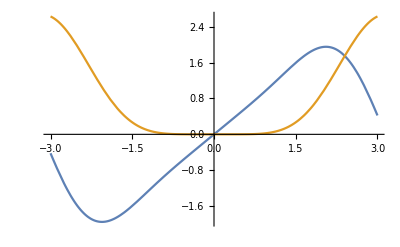

```mathematica
Plot[{Re[w1[kz]],Im[w1[kz]]},{kz,-3,3}]
```

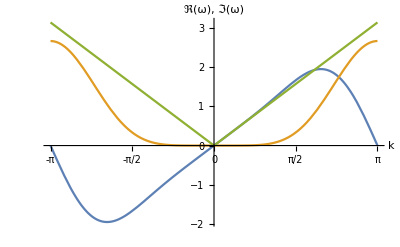

```mathematica
Plot[{Re[w2[kz]],Im[w2[kz]],Norm[kz]},{kz,-π,π},Ticks->{Range[-π,π,π/4],Automatic},AxesLabel->{k,"ℜ(ω), ℑ(ω)"}]
```

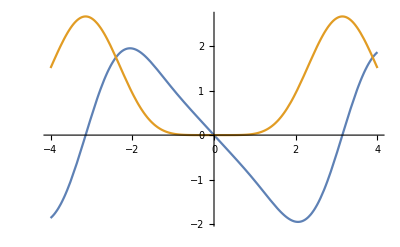

```mathematica
Plot[{Re[w3[kz]],Im[w3[kz]]},{kz,-4,4}]
```

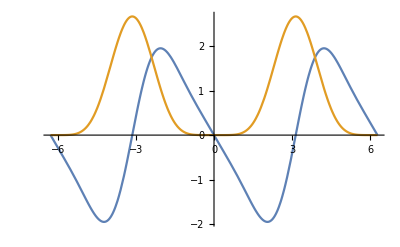

```mathematica
Plot[{Re[w4[kz]],Im[w4[kz]]},{kz,-2π,2π}]
```

Varying Δ we find that as expected the effect increases with larger values and decreases with smaller values (higher resolution). The x-axis scales with Δ^-1 so to say.

The solution from the advanced computational physics lecture 12 does not work, however this one from a paper draft.

```mathematica
ωI[kz_]= Norm[Re[sum[kz]]];
ωR[kz_]= Norm[-Im[sum[kz]]];
```

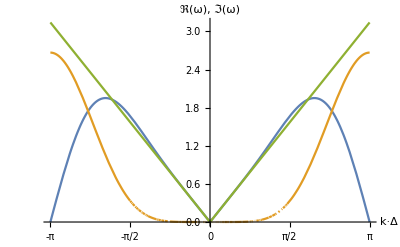

```mathematica
Plot[{ωR[kz],ωI[kz],Norm[kz]},{kz,-π,π},Ticks->{Range[-π,π,π/4],Automatic},AxesLabel->{"k·Δ","ℜ(ω), ℑ(ω)"}]
```

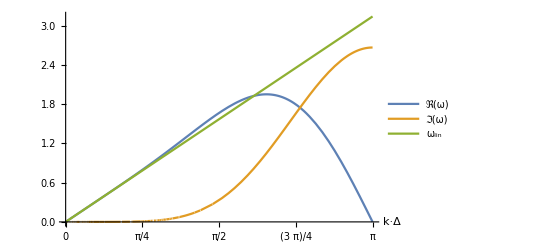

```mathematica
Plot[{ωR[kz],ωI[kz],Norm[kz]},{kz,0,π},Ticks->{Range[0,π,π/4],Automatic},PlotLegends->Placed[{"ℜ(ω)", "ℑ(ω)","ω_lin"},Above],AxesLabel->{"k·Δ",""}]
```

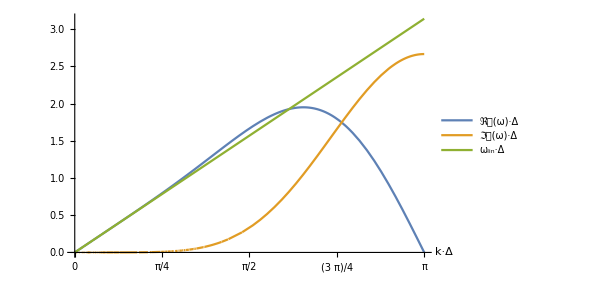

```mathematica
Plot[{ωR[kz],ωI[kz],Norm[kz]},{kz,0,π},Ticks->{Range[0,π,π/4],Automatic},PlotLegends->Placed[{"ℜ𝔢(ω)·Δ", "ℑ𝔪(ω)·Δ","ω_lin·Δ"},{0.2,0.6}],AxesLabel->{"k·Δ",""},
LabelStyle->{FontSize->15,Black}]
```